```mathematica
datastring=Import[NotebookDirectory[]<>"opvalueslong.txt"];
```

```mathematica
header = ImportString[datastring,"Table"][[1;;2]];data=Drop[ImportString[datastring,"Table"],2];
```

```mathematica
header
```

{{},{#,L=,80,beta=,[2.0],t_max=,30.,steps=,2000,D=,[60],#}}

```mathematica
t = data[[All,1]];
energy = data[[All,2]];
mag = data[[All,3]];
```

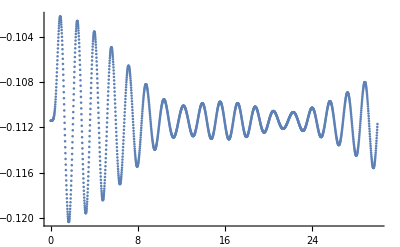

```mathematica
ListPlot[Thread[List[t,mag]]]
```

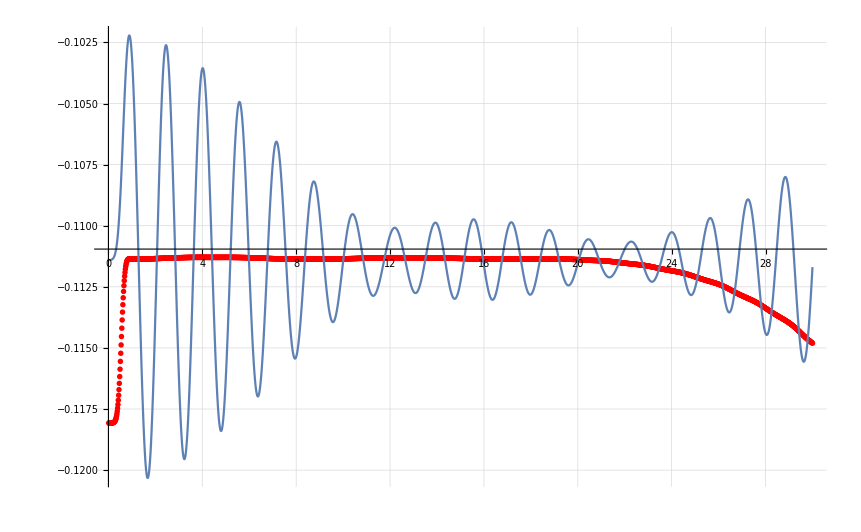

```mathematica
Show[ListPlot[Thread[List[t,((energy-energy[[1000]])+Mean[Drop[mag,1]])]],PlotStyle->Red,PlotRange->Full],ListPlot[Thread[List[t,mag]],Joined->True,PlotRange->Full],PlotRange->Automatic,GridLines->Automatic,ImageSize->Large]
```

```mathematica
ts = TimeSeries[Drop[Thread[{t,mag-Mean[mag[[200;;1500]]]}],1]]
```

TimeSeries[…]

```mathematica
PowerSpectralDensity[ts,ω]
```

8.37531×10^-6+2 (8.36085×10^-6 Cos[ω]+8.31759×10^-6 Cos[2 ω]+8.24569×10^-6 Cos[3 ω]+8.14543×10^-6 Cos[4 ω]+3008+9.86387×10^-11 Cos[1996 ω]+6.14986×10^-11 Cos[1997 ω]+3.25189×10^-11 Cos[1998 ω]+1.19613×10^-11 Cos[1999 ω])
 |  |  |  |

```mathematica
PowerSpectralDensity[ts,ω,HannWindow]
```

8.37531×10^-6+2 (0.+8.36085×10^-6 Cos[ω]+8.31757×10^-6 Cos[2 ω]+8.24564×10^-6 Cos[3 ω]+8.14535×10^-6 Cos[4 ω]+3007+1.41844×10^-15 Cos[1995 ω]+5.48155×10^-16 Cos[1996 ω]+1.51893×10^-16 Cos[1997 ω]+2.00794×10^-17 Cos[1998 ω])
 |  |  |  |

```mathematica
30/2000(0.06/(2Pi))^-1//N
```

1.5708

8.37531×10^-6+2 (0.+8.35667×10^-6 Cos[ω]+8.30925×10^-6 Cos[2 ω]+8.23328×10^-6 Cos[3 ω]+8.12906×10^-6 Cos[4 ω]+3007+5.2286×10^-16 Cos[1995 ω]+2.01958×10^-16 Cos[1996 ω]+5.59344×10^-17 Cos[1997 ω]+7.39048×10^-18 Cos[1998 ω])
 |  |  |  |

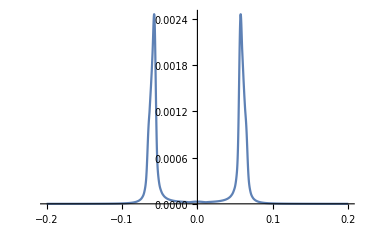

```mathematica
PowerSpectralDensity[ts,ω,HannPoissonWindow]
Plot[%,{ω,-0.2,0.2},PlotRange->Full]
```

```mathematica
FindMaximum[PowerSpectralDensity[ts,ω,HannPoissonWindow],{ω,0.07}]
```

{0.00246108,{ω→0.0573777}}

```mathematica
(t[[1500]]-t[[200]])/1300/(0.0573776546308995/(2Pi))
```

1.64259

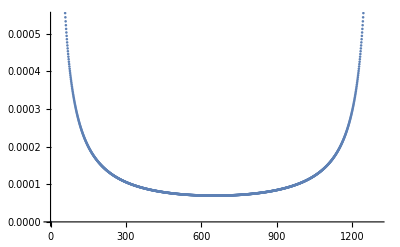

```mathematica
ListPlot[Fourier[Drop[mag[[200;;1500]],1]-Mean[Drop[mag[[200;;1500]],1]]]//Abs]
```

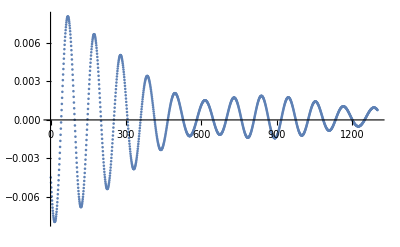

```mathematica
Drop[mag[[200;;1500]],1]-Mean[Drop[mag[[1500;;All]],1]]//ListPlot
```